# Mosquito population dynamics include Early instars, layter instars, pupae, and adults female.

## How to use

Using the code here we can determine seasonal patterns in infection and test the effect of IRS on the mosquito populations. This is a deterministic implementation of the model by White et al. 2011, which itself relies on other references and particularly Griffin et al. 2010. The workflow is to feed the function here the seasonal and or IRS scheme that we want and to take the output and feed it to the parameter file of the ABM. The final vector should be normalized by the predicted abundance without an intervention, to get the amplitude to multiply the biting rate parameter in the model.

White MT, Griffin JT, Churcher TS, Ferguson NM, Basáñez M-G, Ghani AC. Modelling the impact of vector control interventions on Anopheles gambiae population dynamics. Parasit Vectors. 2011;4: 153.

```mathematica
ClearAll[A,P,L,M,K,f,MuM,MuE,MuL, c, TimeMax];
```

## Carrying capacity

145

270

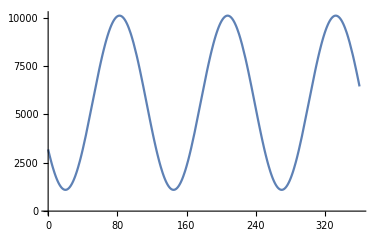

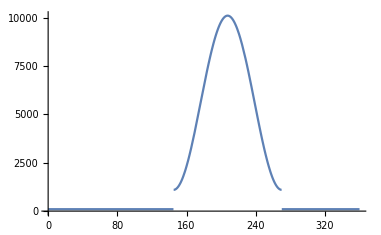

```mathematica
(*
Typically the values would be FirstDayOfRain=160 & LastDayOfRain=270. For the PLOS Biol paper use FirstDayOfRain=145.
*)
FirstDayOfRain=145 (* running day in a year of 360 days where each month is exactly 30 days. For example, 180 will be 30 of June *)
LastDayOfRain=270 (* running day in a year of 360 days where each month is exactly 30 days. For example, 180 will be 30 of June *)

phase=LastDayOfRain- FirstDayOfRain; (*This is the length of the rainy season*)
peakShift=phase*3/4-FirstDayOfRain ; (*This shifts the peak of the sin function towards where peak of rainy season should be.*)
K[t_]:=10000*(0.55+0.45*Sin[2π*(t/phase+peakShift/phase)]); (*Division by phase is to match the phase of the sin function to the seasonality; The value of the sin function is -1 to 1 so its multiplication by 0,45 and the addition of 0.55 is to define a minimum (positive) and a maximum value for the number of mosquitos. *) (* Carrying capacity is just a sin function (this is not from the paper). The width (frequency) is matched to the length of the rainy season. the 10000 is just an arbitrary number. Carrying capacity is just for the first 2 stages (denoted "A" in the ODE model below), as their mortality rates depend on carrying capacity *)
f[t_]:=Piecewise[{{K[t],FirstDayOfRain<Mod[t,360]<LastDayOfRain}},100];  (*Seasonality in carrying capacity. Here, we mimic the Bongo-District seasonality pattern with a short wet season between Jun-Oct (days 180-300) and a prolonged
dry season between Nov-May (days 0-179 and 301-360). In the rainy season, calculate K. Otherwise set to a baseline of 100 *)
Plot[K[t],{t,0,360}]
Plot[f[t],{t,0,360}]
```

## Mortality rates

### Non - adult mortality rates

```mathematica
(* MuE and MuL are the daily mortality of eggs+early larvae and of late larva stages, respectively. 
Both are density-dependent on the number of early and late larva stages, calculated as (A+L)/f, where f is the environmental carrying capacity at time t; 
\mu_E^0 and \mu_L^0 are assumed to be 0.035 and γ = 13.25. These values are taken from Table 1.
The equations are Eq. 7 in the paper.
*)
```

```mathematica
MuE[t_]:=0.035*(1+(A[t]+L[t])/f[t]); 
MuL[t_]:=0.035*(1+13.25*(A[t]+L[t])/f[t]);
```

### Adult mortality rates -- this is the definition of the intervention

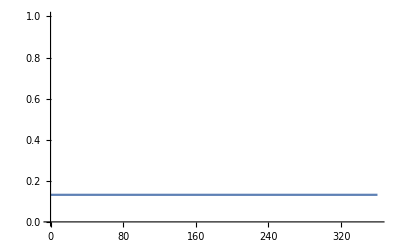

0.8

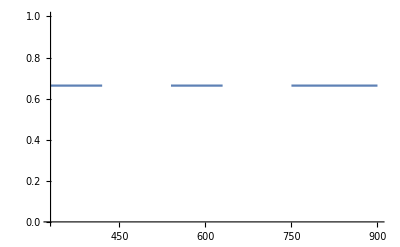

0.9

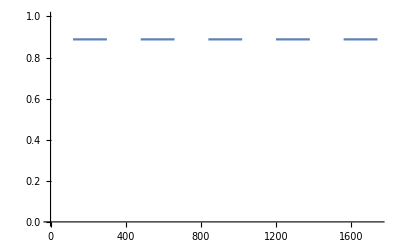

```mathematica
w[c_,Q_,ϕ_,r_,ψ_]:=1-Q*c*ϕ*(1-(1-r)(1-ψ)); (* A function indicating how IRS cahnges the adult mortatlity rate. c is coverge and it is the only parameter here we should change. Parameters and their values are taken from Table S3 in the supplementary information *)

(*MuM is the daily mortality rate of adult mosquitos.The Log turns the w into a rate.*)

(* Example 0: No external mortality rates (no IRS), so c=0 *)
c=0;
TimeMax=360;
MuM [c_,Q_,ϕ_,r_,ψ_,t_]:= {-Log[0.91*w[c,Q,ϕ,r,ψ]*0.74/1-Q *c* ϕ* r*0.74]/3,0<t<TimeMax};
Plot[Evaluate[MuM[0,0.92,0.97,0.207,0.86,t]],{t,0,TimeMax},PlotRange->{0,1}]

(* Example 1: Our Ghana data. Assume c=0.8 *)
c=0.8
MuM [c_,Q_,ϕ_,r_,ψ_,t_]:= Piecewise[{{-Log[0.91*w[c,Q,ϕ,r,ψ]*0.74/1-Q *c* ϕ* r*0.74]/3,330<t<420||540<t<630||750<t<900}},MuM0]; (* The part of 330<t<420||540<t<630||750<t<900 is the IRS scheme of our Ghana data. *)
Plot[Evaluate[MuM[c,0.92,0.97,0.207,0.86,t]],{t,0,1000},PlotRange->{0,1}]


(* Example 2: IRS of 3 months, May-July, with c=0.9, for 5 years *)
c=0.9
TimeMax=5*360;
MuM [c_,Q_,ϕ_,r_,ψ_,t_]:= Piecewise[{{-Log[0.91*w[c,Q,ϕ,r,ψ]*0.74/1-Q *c* ϕ* r*0.74]/3,120<Mod[t,360]<300}},MuM0];
Plot[Evaluate[MuM[c,0.92,0.97,0.207,0.86,t]],{t,0,TimeMax},PlotRange->{0,1}]
(* Plot the mortality rates *)
```

## Mosquito population dynamics without IRS (only seasonality)

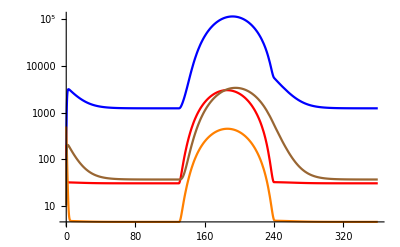

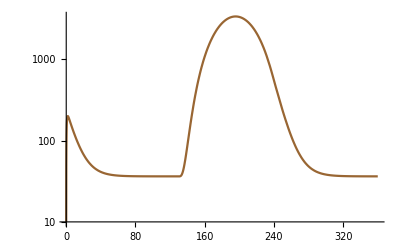

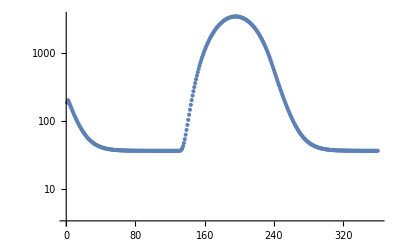

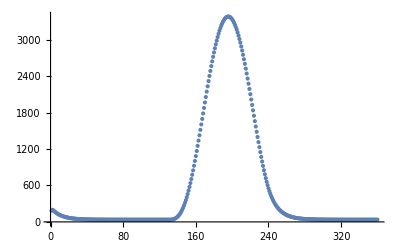

```mathematica
(* When there is no IRS then the mortality rate of adults is just the basline MuM0. This goes in the calculation of M'[t] *)

TimeMax=360;
β=21.19; (* Average number of eggs laid per day; value from Table 1*)
de=6.64; (* length of developmental period of eggs+early larvae in days; the reciprocal of dE is the rate of progression to the next stage; value from Table 1*)
dl=3.72; (* length of developmental period of late larvae in days; Instars that survive development will become pupae at a rate given by the reciprocal of dL; value from Table 1*)
dp=0.64; (*  length of developmental period of pupae, in days; Value from Table 1 *)
MuM0=0.096; (* Daily mortality rate of adult mosquitos; value from Table 1*)
MuP=0.25; (* The pupae daily mortality rate; value ftom Table 1*)
system = {
A'[t] == β* M[t]-A[t]/de-MuE [t]A[t], (*Eggs and early larvae stages*)
L'[t]==A[t]/de-L[t]/dl-MuL[t]*L[t],(*late larvae stages*)
P'[t]==L[t]/dl-P[t]/dp-MuP*P[t], (*Pupae*)
M'[t]==0.5*P[t]/dp-MuM0*M[t], (* Adult mosquitos, half of them are female *)
(* Initial conditions *)
M[0]==10,
A[0]==100,
P[0]==500,
L[0]==200
};
sol = NDSolve[system,{A[t],L[t],P[t],M[t]},{t,0,TimeMax}];
LogPlot[Evaluate[{A[t],L[t],P[t],M[t]}/.sol],{t,0,TimeMax}, PlotStyle->{Blue,Red,Orange,Brown, Purple}] (* Plot abundance of all stages *)
LogPlot[Evaluate[{M[t]}/.sol],{t,0,TimeMax}, PlotStyle->{Brown}] (* Plot abundance of adults *)
MosquitoNoIRS=Table[Evaluate[{M[t]}/.sol],{t,0,TimeMax}];

data=Transpose@{Range[0,TimeMax],Flatten[MosquitoNoIRS,2]};
data=Delete[data,1];
ListLogPlot[data, PlotRange->{0,Max[data]+1}]
ListPlot[data, PlotRange->{0,Max[data]+1}]
Export["~/Documents/malaria_interventions/mosquito_population_plosbiol_2.csv",data];
```

## Mosquito population dynamics with IRS

```mathematica
(* Need to set the IRS scheme, so change these next three lines as necessary, see the examples above *)
w[c_,Q_,ϕ_,r_,ψ_]:=1-Q*c*ϕ*(1-(1-r)(1-ψ)); (* A function indicating how IRS cahnges the adult mortatlity rate. c is coverge and it is the only parameter here we should change. Parameters and their values are taken from Table S3 in the supplementary information *)
FirstDay=120;
LastDay=300;
TimeMax=2*360;
c=0.9;

generateIRS[FirstDay_, LastDay_, TimeMax_, coverage_] := {

filename="~/Documents/malaria_interventions_data/IRS_"<>ToString[FirstDay]<>"_"<>ToString[LastDay]<>"_"<>ToString[coverage]<>"_"<>ToString[TimeMax]<>".csv";
MuM [c_,Q_,ϕ_,r_,ψ_,t_]:= Piecewise[{{-Log[0.91*w[c,Q,ϕ,r,ψ]*0.74/1-Q *c* ϕ* r*0.74]/3,FirstDay<Mod[t,360]<LastDay}},MuM0];

β=21.19; (* Average number of eggs laid per day; value from Table 1*)
de=6.64; (* length of developmental period of eggs+early larvae in days; the reciprocal of dE is the rate of progression to the next stage; value from Table 1*)
dl=3.72; (* length of developmental period of late larvae in days; Instars that survive development will become pupae at a rate given by the reciprocal of dL; value from Table 1*)
     dp=0.64; (*  length of developmental period of pupae, in days; Value from Table 1 *)
MuM0=0.096; (* Daily mortality rate of adult mosquitos; value from Table 1*)
MuP=0.25; (* The pupae daily mortality rate; value ftom Table 1*)
system = {
A'[t] == β* M[t]-A[t]/de-MuE [t]A[t], (*Eggs and early larvae stages*)
L'[t]==A[t]/de-L[t]/dl-MuL[t]*L[t],(*late larvae stages*)
P'[t]==L[t]/dl-P[t]/dp-MuP*P[t], (*Pupae*)
M'[t]==0.5*P[t]/dp-MuM[coverage,0.92,0.97,0.207,0.86,t]*M[t], (*Adult mosquitos, half of them are female*)
(* Initial conditions *)
M[0]==10,
A[0]==100,
P[0]==500,
L[0]==200
};
sol = NDSolve[system,{A[t],L[t],P[t],M[t]},{t,0,TimeMax}];
LogPlot[Evaluate[{A[t],L[t],P[t],M[t]}/.sol],{t,0,TimeMax}, PlotStyle->{Blue,Red,Orange,Brown}]; (* Plot abundance of all stages *)
LogPlot[Evaluate[{M[t]}/.sol],{t,0,TimeMax}, PlotStyle->{Brown}]; (* Plot abundance of adults *)
MosquitoIRS=Table[Evaluate[{M[t]}/.sol],{t,0,TimeMax}];(* Obtain mosquito abundance with intervention*)

data=Transpose@{Range[0,TimeMax],Flatten[MosquitoIRS,2]};
data=Delete[data,1];
Export[filename,data];
data
}
```

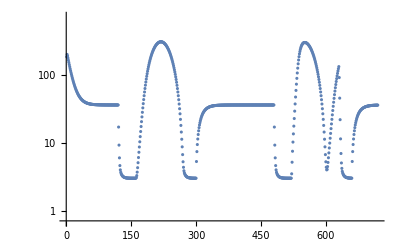

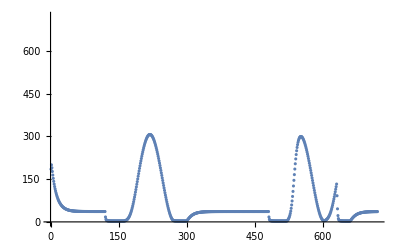

```mathematica
d=generateIRS[120,300,2*360,0.9];
ListLogPlot[d, PlotRange->{0,Max[d]+1}]
ListPlot[d, PlotRange->{0,Max[d]+1}]
```

```mathematica
LengthRange=360*Range[5,20,5];
CoverageRange=Range[0.8,1,0.05];
Table[generateIRS[120,300,a,b],{a,LengthRange},{b,CoverageRange}];
```